## Find absorption probability

```mathematica
q[t] =FullSimplify[Integrate[Sqrt[1/4*Pi*D*t]*Exp[- (x-x0+v*t)^2/(4*D*t)], {x, -Infinity, 0}]]
```

ConditionalExpression[1/2 π √(1/(D t)) (D t)^(3/2) (1+Erf[1/2 √(1/(D t)) (t v-x0)]),(Re[1/(D t)]≥0&&Re[(t v-x0)/(D t)]<0)||Re[1/(D t)]>0]

```mathematica
q[t] = 1/2 π *D*t*(Erfc[1/2 √(1/(D t)) (x0-v*t)])
```

1/2 D π t Erfc[1/2 √(1/(D t)) (-t v+x0)]

## Integrate to get survival probability

```mathematica
lnS[t] = FullSimplify[-Integrate[q[t], t]]
```

$Aborted

```mathematica
S[t] = Exp[%]
```

ConditionalExpression[ⅇ^(-√(π/2) (t+(ⅇ^(-(k (-t v+x0)^2)/(2 D)) √(2/π))/(√(k/D) v)-(√D √(k/D) x0 Erf[(√k (t v-x0))/(√2 √D)])/(√k v)+t Erf[(√(k/D) (t v-x0))/(√2)])),Re[k/D]>0||(Re[k/D]≥0&&Re[(k (t v-x0))/D]<0)]

```mathematica
S[t] = Exp[-√(π/2)t]*Exp [-1/v(√(D/k)ⅇ^(-(k (-t v+x0)^2)/(2 D)) )]*Exp[-√(π/2)1/v(( x0 -vt)*Erf[√(k/(2D))(x0-vt)])]
```

ⅇ^(-√(π/2) t-(ⅇ^(-(k (-t v+x0)^2)/(2 D)) √(D/k))/v-(√(π/2) (-vt+x0) Erf[(√(k/D) (-vt+x0))/(√2)])/v)

## Get first-passage time probability

```mathematica
F[t] = x0/Sqrt[4*Pi*D*t^3] * Exp[-(x0-v*t)^2/(4*D*t)]
```

(ⅇ^(-(-t v+x0)^2/(4 D t)) x0)/(2 √π √(D t^3))

```mathematica
f[t_, x0_, v_, D_] = (ⅇ^(-(-t v+x0)^2/(4 D t)) x0)/(2 √π √(D t^3))
```

(ⅇ^(-(-t v+x0)^2/(4 D t)) x0)/(2 √π √(D t^3))

```mathematica
S[t_, x0_, v_, D_, k_] = Exp[-√(π/2) t-(ⅇ^(-(k (-t* v+x0)^2)/(2 D)) √(D/k))/v-(√(π/2) (-v*t+x0) Erf[(√(k/D) (-v*t+x0))/(√2)])/v ]
```

ⅇ^(-√(π/2) t-(ⅇ^(-(k (-t v+x0)^2)/(2 D)) √(D/k))/v-(√(π/2) (-t v+x0) Erf[(√(k/D) (-t v+x0))/(√2)])/v)

## Scaling of the mean and variance with x0

```mathematica
x0Range = Range[0, 10, 1]
```

{0,1,2,3,4,5,6,7,8,9,10}

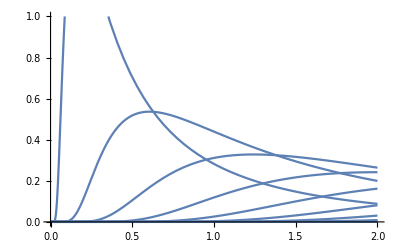

```mathematica
Plot[Thread[f[t,x0Range, 1, 1]],{t,0,2}, PlotRange->{0, 1}]
```

```mathematica
x0means = NIntegrate[t*f[t,x0Range, 1, 1], {t, 0, 100}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

```mathematica
x0var = NIntegrate[t*t*f[t,x0Range,1, 1], {t, 0, 100}] - x0means^2
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.,20.}

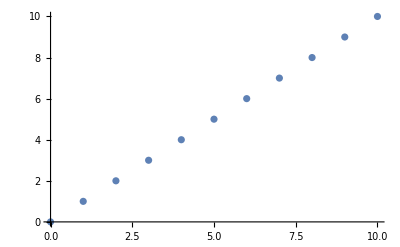

```mathematica
ListPlot[Thread[{x0Range, x0means}]]
```

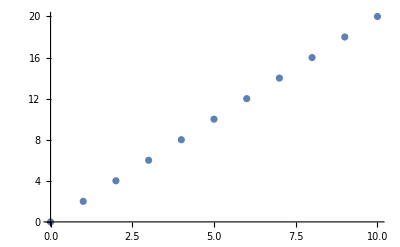

```mathematica
ListPlot[Thread[{x0Range, x0var}]]
```

```mathematica
vRange = Range[1.0, 5.0 , 1]
```

{1.,2.,3.,4.,5.}

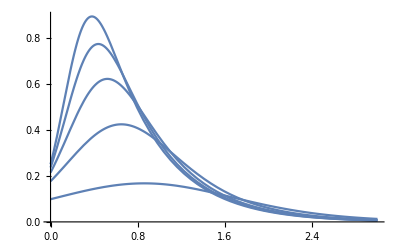

{0.259893,0.0716989,0.0146609,0.00265506,0.000450123}

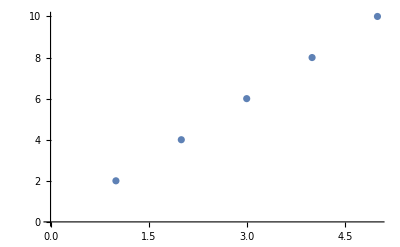

```mathematica
Plot[Thread[f[t,1, vRange, 1, 1]],{t,0,3}]
```